## Neutrino Oscillations in Vacuum Numerical

### Prep

```mathematica
{{Cos[t],Sin[t]},{-Sin[t],Cos[t]}}.{{m1^2,0},{0,m2^2}}.{{Cos[t],-Sin[t]},{Sin[t],Cos[t]}}//FullSimplify
```

{{m1^2 Cos[t]^2+m2^2 Sin[t]^2,(-m1^2+m2^2) Cos[t] Sin[t]},{(-m1^2+m2^2) Cos[t] Sin[t],m2^2 Cos[t]^2+m1^2 Sin[t]^2}}

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/Dropbox/Research/git/15summer/code

### Cal

The parameters

```mathematica
thetaV = 0.2;
omegaV=0.001;
```

Vacuum Hamiltonian in flavor basis is

```mathematica
hamilV=-omegaV{{-Cos[2thetaV],Sin[2thetaV]},{Sin[2thetaV],Cos[2thetaV]}}
```

{{0.000921061,-0.000389418},{-0.000389418,-0.000921061}}

The wavefunction can be written as a vector in flavor basis

```mathematica
nuFV[x_]={nuFVe[x],nuFVx[x]}
```

{nuFVe[x],nuFVx[x]}

The system to be solved is

```mathematica
vacOsc = I nuFV'[x]==hamilV.nuFV[x]
```

{ⅈ nuFVe'[x],ⅈ nuFVx'[x]}=={0.000921061 nuFVe[x]-0.000389418 nuFVx[x],-0.000389418 nuFVe[x]-0.000921061 nuFVx[x]}

```mathematica
solV=DSolve[vacOsc&&nuFV[0]=={1,0},{nuFVe,nuFVx},x]
```

{{nuFVe→Function[{x},(1.02071×10^-17+0.96053 ⅈ) ⅇ^(-3.38813×10^-21 x) ((1.10632×10^-17-0.0410914 ⅈ) Cos[0.001 x]-(0.+1. ⅈ) ⅇ^(3.38813×10^-21 x) Cos[0.001 x]+(0.0410914+1.10632×10^-17 ⅈ) Sin[0.001 x]-(1.+0. ⅈ) ⅇ^(3.38813×10^-21 x) Sin[0.001 x])],nuFVx→Function[{x},(-0.194709-9.93892×10^-17 ⅈ) ⅇ^(-3.38813×10^-21 x) ((-1.+0. ⅈ) Cos[0.001 x]+(1.+0. ⅈ) ⅇ^(3.38813×10^-21 x) Cos[0.001 x]-(0.+1. ⅈ) Sin[0.001 x]-(0.+1. ⅈ) ⅇ^(3.38813×10^-21 x) Sin[0.001 x])]}}

Survival probability of electron neutrinos is

```mathematica
prob=nuFVe/.solV[[1]]
```

Function[{x},(1.02071×10^-17+0.96053 ⅈ) ⅇ^(-3.38813×10^-21 x) ((1.10632×10^-17-0.0410914 ⅈ) Cos[0.001 x]-(0.+1. ⅈ) ⅇ^(3.38813×10^-21 x) Cos[0.001 x]+(0.0410914+1.10632×10^-17 ⅈ) Sin[0.001 x]-(1.+0. ⅈ) ⅇ^(3.38813×10^-21 x) Sin[0.001 x])]

```mathematica
prob[0]
```

1.+1.54074×10^-33 ⅈ

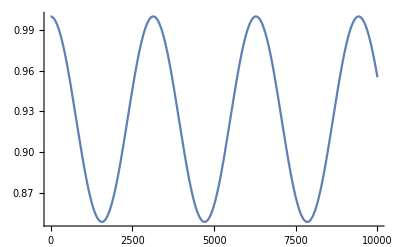

```mathematica
Plot[Abs[prob[x]]^2,{x,0,10000}]
```

### Theoretical Results

The theoretical resutl for survival probability is

```mathematica
probTh[x_]=1-Sin[2thetaV]^2Sin[omegaV*x]^2
```

1-0.151647 Sin[0.001 x]^2

```mathematica
Plot[probTh[x],{x,0,10000}]
```

-Graphics-

Exactly the same.

```mathematica
probTh[test]-(Abs@prob[test])^2/.{test->1800}
```

-3.05311×10^-16

#### Comparison Betwen Numerical And Numerical

```mathematica
Plot[{Abs[prob[x]]^2,probTh[x]},{x,0,10000},Frame->True,ImageSize->Full,PlotLabel->"Survival Probability",FrameLabel->{"Distance/ω","Probability"},PlotLegends->Placed[{"Numerical","Analytical"},{Center,Above}]]
```

-Graphics-

## Vacuum Oscillations with 3 flavors

### Analytical Method

Analytical xxxxx: Hamiltonian should be

```mathematica
pmnsTh={{Cos[Subscript[θ, 12]]Cos[Subscript[θ, 13]],Sin[Subscript[θ, 12]]Cos[Subscript[θ, 13]],Sin[Subscript[θ, 13]]Exp[-I Subscript[δ, CP]]},{-Sin[Subscript[θ, 12]]Cos[Subscript[θ, 23]]-Cos[Subscript[θ, 12]]Sin[Subscript[θ, 23]]Sin[Subscript[θ, 13]]Exp[I Subscript[δ, CP]],Cos[Subscript[θ, 12]]Cos[Subscript[θ, 23]]-Sin[Subscript[θ, 12]]Sin[Subscript[θ, 23]]Sin[Subscript[θ, 13]]Exp[I Subscript[δ, CP]],Sin[Subscript[θ, 23]]Cos[Subscript[θ, 13]]},{Sin[Subscript[θ, 12]]Sin[Subscript[θ, 23]]-Cos[Subscript[θ, 12]]Cos[Subscript[θ, 23]]Sin[Subscript[θ, 13]]Exp[I Subscript[δ, CP]],-Cos[Subscript[θ, 12]]Sin[Subscript[θ, 23]]-Sin[Subscript[θ, 12]]Cos[Subscript[θ, 23]]Sin[Subscript[θ, 13]]Exp[I Subscript[δ, CP]],Cos[Subscript[θ, 23]]Cos[Subscript[θ, 13]]}};
%//MatrixForm
```

(Cos[θ_12] Cos[θ_13] | Cos[θ_13] Sin[θ_12] | ⅇ^(-ⅈ δ_CP) Sin[θ_13]
-Cos[θ_23] Sin[θ_12]-ⅇ^(ⅈ δ_CP) Cos[θ_12] Sin[θ_13] Sin[θ_23] | Cos[θ_12] Cos[θ_23]-ⅇ^(ⅈ δ_CP) Sin[θ_12] Sin[θ_13] Sin[θ_23] | Cos[θ_13] Sin[θ_23]
-ⅇ^(ⅈ δ_CP) Cos[θ_12] Cos[θ_23] Sin[θ_13]+Sin[θ_12] Sin[θ_23] | -ⅇ^(ⅈ δ_CP) Cos[θ_23] Sin[θ_12] Sin[θ_13]-Cos[θ_12] Sin[θ_23] | Cos[θ_13] Cos[θ_23])

To see the point of CP violation phase, we can set it to zero and the matrix becomes unitary imediately. I will use this unitary case in the following case.

```mathematica
Transpose[pmnsTh].pmnsTh/.{Subscript[δ, CP]->0}//FullSimplify//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
pmnsThNCP=pmnsTh/.{Subscript[δ, CP]->0};
%//MatrixForm
```

(Cos[θ_12] Cos[θ_13] | Cos[θ_13] Sin[θ_12] | Sin[θ_13]
-Cos[θ_23] Sin[θ_12]-Cos[θ_12] Sin[θ_13] Sin[θ_23] | Cos[θ_12] Cos[θ_23]-Sin[θ_12] Sin[θ_13] Sin[θ_23] | Cos[θ_13] Sin[θ_23]
-Cos[θ_12] Cos[θ_23] Sin[θ_13]+Sin[θ_12] Sin[θ_23] | -Cos[θ_23] Sin[θ_12] Sin[θ_13]-Cos[θ_12] Sin[θ_23] | Cos[θ_13] Cos[θ_23])

```mathematica
pmnsThNCP.{{Subscript[m, 1]^2,0,0},{0,Subscript[m, 2]^2,0},{0,0,Subscript[m, 3]^2}}.Transpose[pmnsThNCP];
%//FullSimplify
%//MatrixForm
```

{{Cos[θ_13]^2 (Cos[θ_12]^2 m_1^2+Sin[θ_12]^2 m_2^2)+Sin[θ_13]^2 m_3^2,1/2 (Cos[θ_13] Cos[θ_23] Sin[2 θ_12] (-m_1^2+m_2^2)+Sin[2 θ_13] Sin[θ_23] (-Cos[θ_12]^2 m_1^2-Sin[θ_12]^2 m_2^2+m_3^2)),1/2 (Cos[θ_13] Sin[2 θ_12] Sin[θ_23] (m_1^2-m_2^2)+Cos[θ_23] Sin[2 θ_13] (-Cos[θ_12]^2 m_1^2-Sin[θ_12]^2 m_2^2+m_3^2))},{1/2 (Cos[θ_13] Cos[θ_23] Sin[2 θ_12] (-m_1^2+m_2^2)+Sin[2 θ_13] Sin[θ_23] (-Cos[θ_12]^2 m_1^2-Sin[θ_12]^2 m_2^2+m_3^2)),(Cos[θ_23] Sin[θ_12]+Cos[θ_12] Sin[θ_13] Sin[θ_23])^2 m_1^2+(Cos[θ_12] Cos[θ_23]-Sin[θ_12] Sin[θ_13] Sin[θ_23])^2 m_2^2+Cos[θ_13]^2 Sin[θ_23]^2 m_3^2,1/8 (4 Cos[2 θ_23] Sin[2 θ_12] Sin[θ_13] (m_1^2-m_2^2)-2 Cos[2 θ_13] Sin[2 θ_23] (Cos[θ_12]^2 m_1^2+Sin[θ_12]^2 m_2^2-m_3^2)+Sin[2 θ_23] ((-1+3 Cos[2 θ_12]) m_1^2-(1+3 Cos[2 θ_12]) m_2^2+2 m_3^2))},{1/2 (Cos[θ_13] Sin[2 θ_12] Sin[θ_23] (m_1^2-m_2^2)+Cos[θ_23] Sin[2 θ_13] (-Cos[θ_12]^2 m_1^2-Sin[θ_12]^2 m_2^2+m_3^2)),1/8 (4 Cos[2 θ_23] Sin[2 θ_12] Sin[θ_13] (m_1^2-m_2^2)-2 Cos[2 θ_13] Sin[2 θ_23] (Cos[θ_12]^2 m_1^2+Sin[θ_12]^2 m_2^2-m_3^2)+Sin[2 θ_23] ((-1+3 Cos[2 θ_12]) m_1^2-(1+3 Cos[2 θ_12]) m_2^2+2 m_3^2)),(Cos[θ_12] Cos[θ_23] Sin[θ_13]-Sin[θ_12] Sin[θ_23])^2 m_1^2+(Cos[θ_23] Sin[θ_12] Sin[θ_13]+Cos[θ_12] Sin[θ_23])^2 m_2^2+Cos[θ_13]^2 Cos[θ_23]^2 m_3^2}}

```mathematica
hamil3VTh = omegaV pmnsThNCP.{{Subscript[m, 1]^2,0,0},{0,Subscript[m, 2]^2,0},{0,0,Subscript[m, 3]^2}}.Transpose[pmnsThNCP];
%//FullSimplify
%//MatrixForm
```

{{0.001 (Cos[θ_13]^2 (Cos[θ_12]^2 m_1^2+Sin[θ_12]^2 m_2^2)+Sin[θ_13]^2 m_3^2),0.001 Cos[θ_13] (1/2 Cos[θ_23] Sin[2 θ_12] (-m_1^2+m_2^2)+Sin[θ_13] Sin[θ_23] (-Cos[θ_12]^2 m_1^2-Sin[θ_12]^2 m_2^2+m_3^2)),0.0005 Cos[θ_13] (Sin[2 θ_12] Sin[θ_23] (m_1^2-m_2^2)-2 Cos[θ_23] Sin[θ_13] (Cos[θ_12]^2 m_1^2+Sin[θ_12]^2 m_2^2-m_3^2))},{0.001 Cos[θ_13] (1/2 Cos[θ_23] Sin[2 θ_12] (-m_1^2+m_2^2)+Sin[θ_13] Sin[θ_23] (-Cos[θ_12]^2 m_1^2-Sin[θ_12]^2 m_2^2+m_3^2)),0.001 ((Cos[θ_23] Sin[θ_12]+Cos[θ_12] Sin[θ_13] Sin[θ_23])^2 m_1^2+(Cos[θ_12] Cos[θ_23]-Sin[θ_12] Sin[θ_13] Sin[θ_23])^2 m_2^2+Cos[θ_13]^2 Sin[θ_23]^2 m_3^2),0.000125 (4 Cos[2 θ_23] Sin[2 θ_12] Sin[θ_13] (m_1^2-m_2^2)-2 Cos[2 θ_13] Sin[2 θ_23] (Cos[θ_12]^2 m_1^2+Sin[θ_12]^2 m_2^2-m_3^2)+Sin[2 θ_23] ((-1+3 Cos[2 θ_12]) m_1^2-(1+3 Cos[2 θ_12]) m_2^2+2 m_3^2))},{0.0005 Cos[θ_13] (Sin[2 θ_12] Sin[θ_23] (m_1^2-m_2^2)-2 Cos[θ_23] Sin[θ_13] (Cos[θ_12]^2 m_1^2+Sin[θ_12]^2 m_2^2-m_3^2)),0.000125 (4 Cos[2 θ_23] Sin[2 θ_12] Sin[θ_13] (m_1^2-m_2^2)-2 Cos[2 θ_13] Sin[2 θ_23] (Cos[θ_12]^2 m_1^2+Sin[θ_12]^2 m_2^2-m_3^2)+Sin[2 θ_23] ((-1+3 Cos[2 θ_12]) m_1^2-(1+3 Cos[2 θ_12]) m_2^2+2 m_3^2)),0.001 ((Cos[θ_12] Cos[θ_23] Sin[θ_13]-Sin[θ_12] Sin[θ_23])^2 m_1^2+(Cos[θ_23] Sin[θ_12] Sin[θ_13]+Cos[θ_12] Sin[θ_23])^2 m_2^2+Cos[θ_13]^2 Cos[θ_23]^2 m_3^2)}}

(0.001 (Cos[θ_13]^2 (Cos[θ_12]^2 m_1^2+Sin[θ_12]^2 m_2^2)+Sin[θ_13]^2 m_3^2) | 0.001 Cos[θ_13] (1/2 Cos[θ_23] Sin[2 θ_12] (-m_1^2+m_2^2)+Sin[θ_13] Sin[θ_23] (-Cos[θ_12]^2 m_1^2-Sin[θ_12]^2 m_2^2+m_3^2)) | 0.0005 Cos[θ_13] (Sin[2 θ_12] Sin[θ_23] (m_1^2-m_2^2)-2 Cos[θ_23] Sin[θ_13] (Cos[θ_12]^2 m_1^2+Sin[θ_12]^2 m_2^2-m_3^2))
0.001 Cos[θ_13] (1/2 Cos[θ_23] Sin[2 θ_12] (-m_1^2+m_2^2)+Sin[θ_13] Sin[θ_23] (-Cos[θ_12]^2 m_1^2-Sin[θ_12]^2 m_2^2+m_3^2)) | 0.001 ((Cos[θ_23] Sin[θ_12]+Cos[θ_12] Sin[θ_13] Sin[θ_23])^2 m_1^2+(Cos[θ_12] Cos[θ_23]-Sin[θ_12] Sin[θ_13] Sin[θ_23])^2 m_2^2+Cos[θ_13]^2 Sin[θ_23]^2 m_3^2) | 0.000125 (4 Cos[2 θ_23] Sin[2 θ_12] Sin[θ_13] (m_1^2-m_2^2)-2 Cos[2 θ_13] Sin[2 θ_23] (Cos[θ_12]^2 m_1^2+Sin[θ_12]^2 m_2^2-m_3^2)+Sin[2 θ_23] ((-1+3 Cos[2 θ_12]) m_1^2-(1+3 Cos[2 θ_12]) m_2^2+2 m_3^2))
0.0005 Cos[θ_13] (Sin[2 θ_12] Sin[θ_23] (m_1^2-m_2^2)-2 Cos[θ_23] Sin[θ_13] (Cos[θ_12]^2 m_1^2+Sin[θ_12]^2 m_2^2-m_3^2)) | 0.000125 (4 Cos[2 θ_23] Sin[2 θ_12] Sin[θ_13] (m_1^2-m_2^2)-2 Cos[2 θ_13] Sin[2 θ_23] (Cos[θ_12]^2 m_1^2+Sin[θ_12]^2 m_2^2-m_3^2)+Sin[2 θ_23] ((-1+3 Cos[2 θ_12]) m_1^2-(1+3 Cos[2 θ_12]) m_2^2+2 m_3^2)) | 0.001 ((Cos[θ_12] Cos[θ_23] Sin[θ_13]-Sin[θ_12] Sin[θ_23])^2 m_1^2+(Cos[θ_23] Sin[θ_12] Sin[θ_13]+Cos[θ_12] Sin[θ_23])^2 m_2^2+Cos[θ_13]^2 Cos[θ_23]^2 m_3^2))

I could take out an identity matrix but it takes time. It doens’t really matter anyway. So I’ll use this form of Hamiltonian.

```mathematica
nuF3VTh[x_]={nuF3VeTh[x],nuF3VmTh[x],nuF3VtTh[x]}
```

{nuF3VeTh[x],nuF3VmTh[x],nuF3VtTh[x]}

```mathematica
vacOsc3Th = I nuF3VTh'[x]==hamil3VTh.nuF3VTh[x]
```

{ⅈ nuF3VeTh'[x],ⅈ nuF3VmTh'[x],ⅈ nuF3VtTh'[x]}=={0.001 nuF3VtTh[x] (Cos[θ_12] Cos[θ_13] (-Cos[θ_12] Cos[θ_23] Sin[θ_13]+Sin[θ_12] Sin[θ_23]) m_1^2+Cos[θ_13] Sin[θ_12] (-Cos[θ_23] Sin[θ_12] Sin[θ_13]-Cos[θ_12] Sin[θ_23]) m_2^2+Cos[θ_13] Cos[θ_23] Sin[θ_13] m_3^2)+0.001 nuF3VeTh[x] (Cos[θ_12]^2 Cos[θ_13]^2 m_1^2+Cos[θ_13]^2 Sin[θ_12]^2 m_2^2+Sin[θ_13]^2 m_3^2)+0.001 nuF3VmTh[x] (Cos[θ_12] Cos[θ_13] (-Cos[θ_23] Sin[θ_12]-Cos[θ_12] Sin[θ_13] Sin[θ_23]) m_1^2+Cos[θ_13] Sin[θ_12] (Cos[θ_12] Cos[θ_23]-Sin[θ_12] Sin[θ_13] Sin[θ_23]) m_2^2+Cos[θ_13] Sin[θ_13] Sin[θ_23] m_3^2),0.001 nuF3VtTh[x] ((-Cos[θ_12] Cos[θ_23] Sin[θ_13]+Sin[θ_12] Sin[θ_23]) (-Cos[θ_23] Sin[θ_12]-Cos[θ_12] Sin[θ_13] Sin[θ_23]) m_1^2+(-Cos[θ_23] Sin[θ_12] Sin[θ_13]-Cos[θ_12] Sin[θ_23]) (Cos[θ_12] Cos[θ_23]-Sin[θ_12] Sin[θ_13] Sin[θ_23]) m_2^2+Cos[θ_13]^2 Cos[θ_23] Sin[θ_23] m_3^2)+0.001 nuF3VeTh[x] (Cos[θ_12] Cos[θ_13] (-Cos[θ_23] Sin[θ_12]-Cos[θ_12] Sin[θ_13] Sin[θ_23]) m_1^2+Cos[θ_13] Sin[θ_12] (Cos[θ_12] Cos[θ_23]-Sin[θ_12] Sin[θ_13] Sin[θ_23]) m_2^2+Cos[θ_13] Sin[θ_13] Sin[θ_23] m_3^2)+0.001 nuF3VmTh[x] ((-Cos[θ_23] Sin[θ_12]-Cos[θ_12] Sin[θ_13] Sin[θ_23])^2 m_1^2+(Cos[θ_12] Cos[θ_23]-Sin[θ_12] Sin[θ_13] Sin[θ_23])^2 m_2^2+Cos[θ_13]^2 Sin[θ_23]^2 m_3^2),0.001 nuF3VtTh[x] ((-Cos[θ_12] Cos[θ_23] Sin[θ_13]+Sin[θ_12] Sin[θ_23])^2 m_1^2+(-Cos[θ_23] Sin[θ_12] Sin[θ_13]-Cos[θ_12] Sin[θ_23])^2 m_2^2+Cos[θ_13]^2 Cos[θ_23]^2 m_3^2)+0.001 nuF3VeTh[x] (Cos[θ_12] Cos[θ_13] (-Cos[θ_12] Cos[θ_23] Sin[θ_13]+Sin[θ_12] Sin[θ_23]) m_1^2+Cos[θ_13] Sin[θ_12] (-Cos[θ_23] Sin[θ_12] Sin[θ_13]-Cos[θ_12] Sin[θ_23]) m_2^2+Cos[θ_13] Cos[θ_23] Sin[θ_13] m_3^2)+0.001 nuF3VmTh[x] ((-Cos[θ_12] Cos[θ_23] Sin[θ_13]+Sin[θ_12] Sin[θ_23]) (-Cos[θ_23] Sin[θ_12]-Cos[θ_12] Sin[θ_13] Sin[θ_23]) m_1^2+(-Cos[θ_23] Sin[θ_12] Sin[θ_13]-Cos[θ_12] Sin[θ_23]) (Cos[θ_12] Cos[θ_23]-Sin[θ_12] Sin[θ_13] Sin[θ_23]) m_2^2+Cos[θ_13]^2 Cos[θ_23] Sin[θ_23] m_3^2)}

```mathematica
sol3VTh=DSolve[vacOsc3Th&&nuF3VTh[0]=={1,0,0},{nuF3VeTh,nuF3VmTh,nuF3VtTh},x]
```

```mathematica
prob3Th=nuF3VeTh/.sol3VTh[[1]]
```

### Numerical Method

mixing angle data

```mathematica
theta12=33.36/180*Pi;
theta13=8.66/180*Pi;
theta23=40/180*Pi;
deltacp=0;
(*deltacp=300/180*Pi;*)
m1sq=0.01;
m2sq=m1sq+0.000079;
oneFourE=100;
```

The PMNS matrix is

```mathematica
pmns={{Cos[theta12]Cos[theta13],Sin[theta12]Cos[theta13],Sin[theta13]Exp[-I deltacp]},{-Sin[theta12]Cos[theta23]-Cos[theta12]Sin[theta23]Sin[theta13]Exp[I deltacp],Cos[theta12]Cos[theta23]-Sin[theta12]Sin[theta23]Sin[theta13]Exp[I deltacp],Sin[theta23]Cos[theta13]},{Sin[theta12]Sin[theta23]-Cos[theta12]Cos[theta23]Sin[theta13]Exp[I deltacp],-Cos[theta12]Sin[theta23]-Sin[theta12]Cos[theta23]Sin[theta13]Exp[I deltacp],Cos[theta23]Cos[theta13]}}
%//MatrixForm
```

{{0.82571,0.543629,0.150571},{-0.502084,0.586603,0.635459},{0.257129,-0.600304,0.757311}}

(0.82571 | 0.543629 | 0.150571
-0.502084 | 0.586603 | 0.635459
0.257129 | -0.600304 | 0.757311)

#### Normal Hierarchy

The mass squared of the third is

```mathematica
m3sq=m2sq+0.0027;
```

Hamiltonian is

```mathematica
hamil3V=oneFourE pmns.{{m1sq,0,0},{0,m2sq,0},{0,0,m3sq}}.Transpose[pmns];
```

```mathematica
nuF3V[x_]={nuF3Ve[x],nuF3Vm[x],nuF3Vt[x]}
```

{nuF3Ve[x],nuF3Vm[x],nuF3Vt[x]}

```mathematica
vacOsc3 = I nuF3V'[x]==hamil3V.nuF3V[x]
```

{ⅈ nuF3Ve'[x],ⅈ nuF3Vm'[x],ⅈ nuF3Vt'[x]}=={1.00864 nuF3Ve[x]+0.0291092 nuF3Vm[x]+0.0291105 nuF3Vt[x],0.0291092 nuF3Ve[x]+1.11494 nuF3Vm[x]+0.130955 nuF3Vt[x],0.0291105 nuF3Ve[x]+0.130955 nuF3Vm[x]+1.16223 nuF3Vt[x]}

```mathematica
sol3V=DSolve[vacOsc3&&nuF3V[0]=={1,0,0},{nuF3Ve,nuF3Vm,nuF3Vt},x]
```

{{nuF3Ve→Function[{x},(0.0226715+5.74892×10^-18 ⅈ) ⅇ^(-2.19551×10^-17 x) ((30.0728+2.31695×10^-14 ⅈ) ⅇ^(2.19556×10^-17 x) Cos[1. x]+(13.0354-3.43542×10^-14 ⅈ) Cos[1.0079 x]+(1.+0. ⅈ) ⅇ^(2.19551×10^-17 x) Cos[1.2779 x]+(2.31695×10^-14-30.0728 ⅈ) ⅇ^(2.19556×10^-17 x) Sin[1. x]-(3.43542×10^-14+13.0354 ⅈ) Sin[1.0079 x]-(0.+1. ⅈ) ⅇ^(2.19551×10^-17 x) Sin[1.2779 x])],nuF3Vm→Function[{x},(0.0956815+1.05011×10^-17 ⅈ) ⅇ^(-2.19551×10^-17 x) ((-4.33287+1.30434×10^-15 ⅈ) ⅇ^(2.19556×10^-17 x) Cos[1. x]+(3.33287-1.30434×10^-15 ⅈ) Cos[1.0079 x]+(1.+0. ⅈ) ⅇ^(2.19551×10^-17 x) Cos[1.2779 x]+(1.30434×10^-15+4.33287 ⅈ) ⅇ^(2.19556×10^-17 x) Sin[1. x]-(1.30434×10^-15+3.33287 ⅈ) Sin[1.0079 x]-(0.+1. ⅈ) ⅇ^(2.19551×10^-17 x) Sin[1.2779 x])],nuF3Vt→Function[{x},(0.114029+2.09755×10^-17 ⅈ) ⅇ^(-2.19551×10^-17 x) ((1.86193-2.19626×10^-15 ⅈ) ⅇ^(2.19556×10^-17 x) Cos[1. x]-(2.86193-2.19626×10^-15 ⅈ) Cos[1.0079 x]+(1.+0. ⅈ) ⅇ^(2.19551×10^-17 x) Cos[1.2779 x]-(2.19626×10^-15+1.86193 ⅈ) ⅇ^(2.19556×10^-17 x) Sin[1. x]+(2.19626×10^-15+2.86193 ⅈ) Sin[1.0079 x]-(0.+1. ⅈ) ⅇ^(2.19551×10^-17 x) Sin[1.2779 x])]}}

```mathematica
prob3=nuF3Ve/.sol3V[[1]]
```

Function[{x},(0.0226715+5.74892×10^-18 ⅈ) ⅇ^(-2.19551×10^-17 x) ((30.0728+2.31695×10^-14 ⅈ) ⅇ^(2.19556×10^-17 x) Cos[1. x]+(13.0354-3.43542×10^-14 ⅈ) Cos[1.0079 x]+(1.+0. ⅈ) ⅇ^(2.19551×10^-17 x) Cos[1.2779 x]+(2.31695×10^-14-30.0728 ⅈ) ⅇ^(2.19556×10^-17 x) Sin[1. x]-(3.43542×10^-14+13.0354 ⅈ) Sin[1.0079 x]-(0.+1. ⅈ) ⅇ^(2.19551×10^-17 x) Sin[1.2779 x])]

```mathematica
Abs@prob3[0]
Abs@prob3[1]
```

1.

0.999158

```mathematica
prob3e=nuF3Ve/.sol3V[[1]]
prob3m=nuF3Vm/.sol3V[[1]]
prob3t=nuF3Vt/.sol3V[[1]]
```

Function[{x},(0.0226715+5.74892×10^-18 ⅈ) ⅇ^(-2.19551×10^-17 x) ((30.0728+2.31695×10^-14 ⅈ) ⅇ^(2.19556×10^-17 x) Cos[1. x]+(13.0354-3.43542×10^-14 ⅈ) Cos[1.0079 x]+(1.+0. ⅈ) ⅇ^(2.19551×10^-17 x) Cos[1.2779 x]+(2.31695×10^-14-30.0728 ⅈ) ⅇ^(2.19556×10^-17 x) Sin[1. x]-(3.43542×10^-14+13.0354 ⅈ) Sin[1.0079 x]-(0.+1. ⅈ) ⅇ^(2.19551×10^-17 x) Sin[1.2779 x])]

Function[{x},(0.0956815+1.05011×10^-17 ⅈ) ⅇ^(-2.19551×10^-17 x) ((-4.33287+1.30434×10^-15 ⅈ) ⅇ^(2.19556×10^-17 x) Cos[1. x]+(3.33287-1.30434×10^-15 ⅈ) Cos[1.0079 x]+(1.+0. ⅈ) ⅇ^(2.19551×10^-17 x) Cos[1.2779 x]+(1.30434×10^-15+4.33287 ⅈ) ⅇ^(2.19556×10^-17 x) Sin[1. x]-(1.30434×10^-15+3.33287 ⅈ) Sin[1.0079 x]-(0.+1. ⅈ) ⅇ^(2.19551×10^-17 x) Sin[1.2779 x])]

Function[{x},(0.114029+2.09755×10^-17 ⅈ) ⅇ^(-2.19551×10^-17 x) ((1.86193-2.19626×10^-15 ⅈ) ⅇ^(2.19556×10^-17 x) Cos[1. x]-(2.86193-2.19626×10^-15 ⅈ) Cos[1.0079 x]+(1.+0. ⅈ) ⅇ^(2.19551×10^-17 x) Cos[1.2779 x]-(2.19626×10^-15+1.86193 ⅈ) ⅇ^(2.19556×10^-17 x) Sin[1. x]+(2.19626×10^-15+2.86193 ⅈ) Sin[1.0079 x]-(0.+1. ⅈ) ⅇ^(2.19551×10^-17 x) Sin[1.2779 x])]

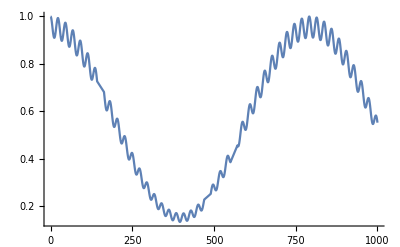

```mathematica
normalPlt=Plot[(Abs@prob3[x])^2,{x,0,1000}]
```

#### Inverted Hierarchy

The mass squared of the third is

```mathematica
m3sqInv=m2sq-0.0027;
```

Hamiltonian is

```mathematica
hamil3VInv=oneFourE pmns.{{m1sq,0,0},{0,m2sq,0},{0,0,m3sqInv}}.Transpose[pmns];
```

```mathematica
nuF3VInv[x_]={nuF3VeInv[x],nuF3VmInv[x],nuF3VtInv[x]}
```

{nuF3VeInv[x],nuF3VmInv[x],nuF3VtInv[x]}

```mathematica
vacOsc3Inv = I nuF3VInv'[x]==hamil3VInv.nuF3VInv[x]
```

{ⅈ nuF3VeInv'[x],ⅈ nuF3VmInv'[x],ⅈ nuF3VtInv'[x]}=={0.996392 nuF3VeInv[x]-0.0225589 nuF3VmInv[x]-0.0324651 nuF3VtInv[x],-0.0225589 nuF3VeInv[x]+0.89688 nuF3VmInv[x]-0.128915 nuF3VtInv[x],-0.0324651 nuF3VeInv[x]-0.128915 nuF3VmInv[x]+0.852527 nuF3VtInv[x]}

```mathematica
sol3VInv=DSolve[vacOsc3Inv&&nuF3VInv[0]=={1,0,0},{nuF3VeInv,nuF3VmInv,nuF3VtInv},x]
```

{{nuF3VeInv→Function[{x},(0.0226715+9.58735×10^-18 ⅈ) ⅇ^(-4.44089×10^-16 x) ((1.+0. ⅈ) ⅇ^(5.55112×10^-16 x) Cos[0.7379 x]+(30.0728+1.53039×10^-14 ⅈ) Cos[1. x]+(13.0354-3.39564×10^-14 ⅈ) ⅇ^(5.95644×10^-16 x) Cos[1.0079 x]-(0.+1. ⅈ) ⅇ^(5.55112×10^-16 x) Sin[0.7379 x]+(1.53039×10^-14-30.0728 ⅈ) Sin[1. x]-(3.39564×10^-14+13.0354 ⅈ) ⅇ^(5.95644×10^-16 x) Sin[1.0079 x])],nuF3VmInv→Function[{x},(0.0956815+2.19974×10^-17 ⅈ) ⅇ^(-4.44089×10^-16 x) ((1.+0. ⅈ) ⅇ^(5.55112×10^-16 x) Cos[0.7379 x]-(4.33287-5.49345×10^-16 ⅈ) Cos[1. x]+(3.33287-5.49345×10^-16 ⅈ) ⅇ^(5.95644×10^-16 x) Cos[1.0079 x]-(0.+1. ⅈ) ⅇ^(5.55112×10^-16 x) Sin[0.7379 x]+(5.49345×10^-16+4.33287 ⅈ) Sin[1. x]-(5.49345×10^-16+3.33287 ⅈ) ⅇ^(5.95644×10^-16 x) Sin[1.0079 x])],nuF3VtInv→Function[{x},(0.114029+2.67876×10^-17 ⅈ) ⅇ^(-4.44089×10^-16 x) ((1.+0. ⅈ) ⅇ^(5.55112×10^-16 x) Cos[0.7379 x]+(1.86193-1.4654×10^-15 ⅈ) Cos[1. x]-(2.86193-1.4654×10^-15 ⅈ) ⅇ^(5.95644×10^-16 x) Cos[1.0079 x]-(0.+1. ⅈ) ⅇ^(5.55112×10^-16 x) Sin[0.7379 x]-(1.4654×10^-15+1.86193 ⅈ) Sin[1. x]+(1.4654×10^-15+2.86193 ⅈ) ⅇ^(5.95644×10^-16 x) Sin[1.0079 x])]}}

```mathematica
prob3Inv=nuF3VeInv/.sol3VInv[[1]]
```

Function[{x},(0.0226715+9.58735×10^-18 ⅈ) ⅇ^(-4.44089×10^-16 x) ((1.+0. ⅈ) ⅇ^(5.55112×10^-16 x) Cos[0.7379 x]+(30.0728+1.53039×10^-14 ⅈ) Cos[1. x]+(13.0354-3.39564×10^-14 ⅈ) ⅇ^(5.95644×10^-16 x) Cos[1.0079 x]-(0.+1. ⅈ) ⅇ^(5.55112×10^-16 x) Sin[0.7379 x]+(1.53039×10^-14-30.0728 ⅈ) Sin[1. x]-(3.39564×10^-14+13.0354 ⅈ) ⅇ^(5.95644×10^-16 x) Sin[1.0079 x])]

```mathematica
Abs@prob3Inv[0]
Abs@prob3Inv[1]
```

1.

0.999223

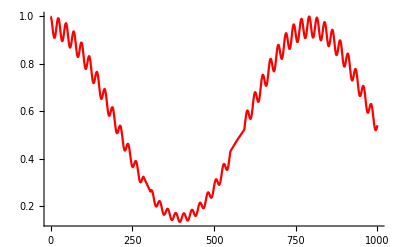

```mathematica
invertedPlt=Plot[(Abs@prob3Inv[x])^2,{x,0,1000},PlotStyle->Red]
```

#### Comparing the two hierarchies

```mathematica
Plot[{(Abs@prob3Inv[x])^2,(Abs@prob3[x])^2},{x,0,1000},FrameLabel->{"Distance/ω","Probability"},PlotLabel->"Comparing Normal Hierarchy and Inverted Hierarchy",ImageSize->Full,Frame->True,PlotLegends->Placed[{"Inverted Hierarchy","Normal Hierarchy"},{Center,Above}]]
```

-Graphics-

#### Export Data to tab data

-Graphics-

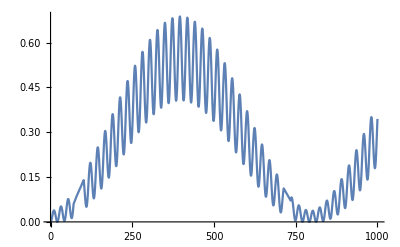

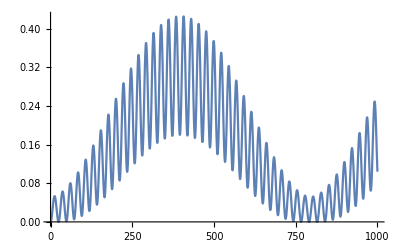

```mathematica
normalPlte=Plot[(Abs@prob3e[x])^2,{x,0,1000}]
normalPltm=Plot[(Abs@prob3m[x])^2,{x,0,1000}]
normalPltt=Plot[(Abs@prob3t[x])^2,{x,0,1000}]
```

```mathematica
terneryData=Table[{(Abs@prob3e[x])^2,(Abs@prob3m[x])^2,(Abs@prob3t[x])^2},{x,1,1000}];
```

```mathematica
Export["terneryData.txt",terneryData,"CSV"]
```

terneryData.txt